# Simon’s Algorithm

Episode 29. Deutsch-Jozsa Algorithm

Episode 30. Bernstein-Vazirani Algorithm

Episode 31. Simon’s Algorithm

## Statement of the Problem

We are given a function f:{0, 1}^n→{0, 1}^n and a secret string s of n bits.

-Graphics-

For all x,y∈{0,1}^n, f(x)=f(y) if and only if y=x⊕s.

Note that f is either one-to-one (s=0) or two-to-one (s≠0).

The task is to find the secret string s with as few queries to function f as possible.

Classically, one needs queries to f(x) with up to 2^(n-1)+1 different inputs.

## Quantum Implementation

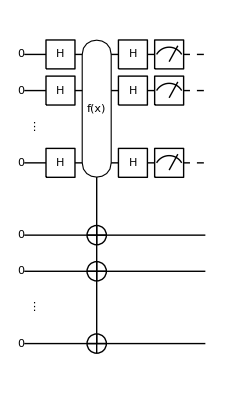

Figure 1. A quantum circuit to implement Simon's algorithm.

For the analysis of the quantum circuit, see Section 4.2.4 of the Quantum Workbook (2022, 2023) or the Q3 tutorial “Simon’s Algorithm”.

## Examples

```mathematica
Let[Qubit,S,T]
```

### Smaller System

Consider again a secrete bit string.

```mathematica
string={1,1};
```

Consider a two-to-one function obeying the rule (specified in Simon’s problem).

```mathematica
Clear[f];
f[{0,0}]=f[{1,1}]={0,1};
f[{0,1}]=f[{1,0}]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
qc=QuantumCircuit[
Ket[S@{1,2}->0,T@{1,2}->0],
S[{1,2},6],
Oracle[f,S@{1,2},T@{1,2}],
S[{1,2},6],
Measurement[S[{1,2},3]],
"Invisible"->S@{2.5}
]
```

```mathematica
out=ExpressionFor[qc]
result=Readout[S[{1,2},3]]
```

```mathematica
mat=Table[ExpressionFor[qc];Readout[S[{1,2},3]],{2}]
```

### Larger System

```mathematica
Let[Qubit,S,T]
```

Now, let us examine a lager system.

```mathematica
$n=3;
kk=Range[$n]
```

Suppose that we are given a secrete bit string.

```mathematica
string={1,1,0};
```

This is a function consistent with the above secrete bit string.

```mathematica
Clear[f];
f[0]=f[6]=3;
f[1]=f[7]=7;
f[2]=f[4]=4;
f[3]=f[5]=1;
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
qc1=QuantumCircuit[
Ket[S@kk->0,T@kk->0],
S[kk,6],Oracle[f,S@kk,T@kk],S[kk,6],
"Invisible"->S@{3.5}
]
```

```mathematica
qc2=QuantumCircuit[qc1,Measurement[S[kk,3]]]
```

Get the measurement outcome.

```mathematica
out=ExpressionFor[qc2]
result=Readout[S[kk,3]]
```

To make repeated measurements, it is more efficient to first compute the state just before the measurement.

```mathematica
new=ExpressionFor[qc1];
```

Now, perform the measurement repeatedly.

```mathematica
data=Table[Measurement[S[kk,3]]@new;Readout[S[kk,3]],{12}];
data//TableForm
```

As two linearly independent vectors (bit strings), we choose these:

```mathematica
mat={{1,1,0},{0,0,1}}
```

Then, the linear equation, mat.ss=0 (mod 2), for the Boolean variables ss:={s1,s2,s3} is given by the following, which agrees with the given secrete bit string.

```mathematica
ss={1,1,0}
```

```mathematica
Mod[mat.ss,2]
```

## Summary

### Keywords

Oracle

Decision making

Simon’s problem

### Functions

Oracle

### Related Links

Section 4.2 of the Quantum Workbook (2022, 2023).

Tutorial: Simon's Algorithm